# Balanced Worst Case distribution

Estimating exact future returns is impossible.

Estimating a distribution, meaning estimating the parameters that define the distribution (e.g. μ and σ in case of the beloved gauss curve) is hard.

This article instead looks the balanced-worst-case distribution, which is the worst possible distribution for a given strategy with the only restriction being that P(S < x) = 0.5, meaning half of the points are left of x and half of the points are to the right of x.

### What is the Balanced Worst Case distribution

Imagine you have a strategy that is so robust that even if everything goes wrong, you make money (or at least don’t go bust). One way to test the robustness of a strategy is therefore to find what would be the rate of returns assuming that the strategy always has the worst possible results. 

Example
- If your strategy is holding stock, then the worst case distribution is when the stock is always falling. Every single time.
- If your strategy is holding stocks + long OTM puts (e.g. insurance), the worst case is going to be when the puts expire worthless.

Chances are that no strategy worth pursuing will pass this test, so let’s relax our overly strict test a bit by adding an additional restriction on the worst-case distribution. The new restriction is that the distribution must be balanced, meaning that half of the returns will land on the left and half of the returns will land on the right. More formally P(S<x)=0.5 and P(S>x)=0.5. 

Example
- If your strategy is holding stock and assuming the distribution is centered at 0, then the balanced worst case distribution is one where half of the returns are very negative (say -0.5) and half of the returns are at 0.

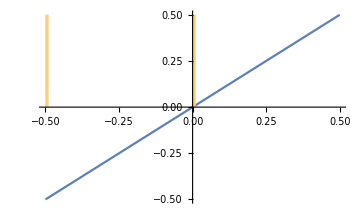

```mathematica
Show[{Plot[s,{s,-0.5,0.5}, ImageSize->Medium],Histogram[{-0.5,0},{0.01},"Probability", ImageSize->Medium] }]
```

Example
Assuming you hold stock and OTM puts with a strike of -0.10 and assuming the returns are centered around 0.

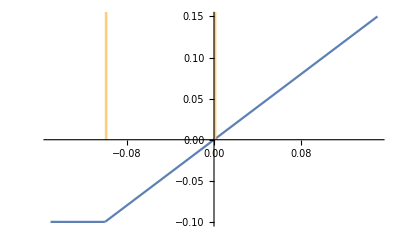

```mathematica
Show[{
Plot[s+Max[-0.1-s,0],{s,-0.15,0.15}],
Histogram[{-0.1,0},{0.002},"Probability"]
}]
```

Example
You hold the following position: 1 long stock, 1 short ATM call, 1 OTM put

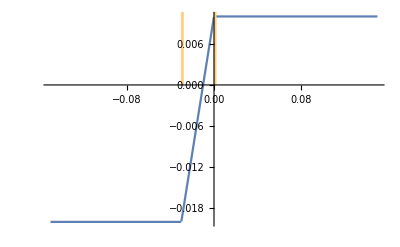

```mathematica
Show[{
Plot[s+Max[-0.03-s,0]-Max[s,0]+0.01,{s,-0.15,0.15}],
Histogram[{-0.03,0},{0.002},"Probability"]
}]
```

### Calculating the geometric mean

Once we have a distribution and a payoff function we can calculate the geometric mean of a payoff function as follows:

Let payoff(s) denote a payoff function as a function of the spot.
Let the set {r_left, r_right} denote the balanced worst case distribution  where P(S=r_left)=p and P(S=r_right)=1-p

Then the geometric mean is simply

Ĝ= (payoff(r_left))^p (payoff(r_right))^(1-p)

### How realistic is the assumption that assets might be balanced?

Let’s validate this assumption by looking at the 1-day returns of SPY and QQQ over periods of 100 days.

```mathematica
dateRange = {Today-Quantity[20,"Years"], Today, "Weekly"};
pricesAmzn = Normal[FinancialData["NASDAQ:AMZN","Return",dateRange]["Values"]];
pricesSpy = Normal[FinancialData["NYSE:SPY","Return",dateRange]["Values"]];
pricesQqq = Normal[FinancialData["NASDAQ:QQQ","Return",dateRange]["Values"]];
```

```mathematica
CalcProbabilityBalanced[prices_, days_]:=Table[
With[
{priceSequence = EmpiricalDistribution[prices[[i;;i+days]]]},
NProbability[x>0 , x\[Distributed]priceSequence]
],
{i,1,Length[prices]-days,Ceiling[days/5]}
]
```

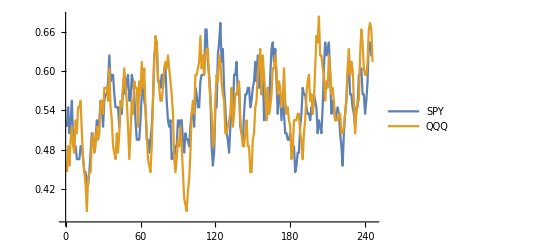

```mathematica
Map[CalcProbabilityBalanced[#,100]&,{pricesSpy, pricesQqq}]//ListLinePlot[#,{PlotLegends->{"SPY","QQQ"}}]&
```

The graph above plots, the probability of the n-th 100-day period being balanced. Let’s now look at the survival functions, meaning what is the probability that a 100-day period was balanced. We can see that the probability of a 100-day period being balanced  has a probability of approximately 0.8.

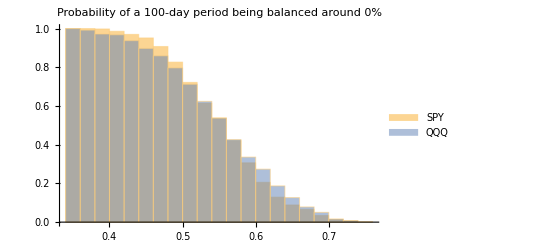

```mathematica
Map[CalcProbabilityBalanced[#,50]&,{pricesSpy, pricesQqq}]//Histogram[#, Automatic, "SF", {PlotLabel->"Probability of a 100-day period being balanced around 0%", ChartLegends->{"SPY","QQQ"}}]&
```

```mathematica
options = Import["~/Downloads/2020-11-19.spy.json"]//
Map[Association]//
Map[
Append[#,{
"relativeStrike"->#[["strike"]]/#[["spotPrice"]],

"callRelativePrice"->(#[["callBid"]]+#[["callAsk"]])/(2 *#[["spotPrice"]]),

"putRelativePrice"->(#[["putBid"]]+#[["putAsk"]])/(2 *#[["spotPrice"]])
}]
&];
```

```mathematica
IsAtTheMoney[opt_]:=Abs[opt["strike"]-opt["spotPrice"]]<0.9;
IsAtTheMoney::usage = "IsAtTheMoney[option] returns true if the option is at the money.";


IsPutOtm[opt_]:=opt["strike"]<opt["spotPrice"];
IsPutOtm::usage = "IsPutOtm[option] returns true if the put is out of the money.";


SplitByDays[opts_]:=opts//GroupBy[#days&]//Values;
SplitByDays::usage = "SplitByDays[options] splits the given option chain by days.";


Combinations[listA_, listB_]:=Outer[{#1,#2}&,listA,listB]//Flatten[#,1]&;
Combinations::usage = "Combinations[listA, listB] 
returns a list of tuples where each tuple {a,b} has an element in listA and listB

Examples:

Combinations[{a,b},{1,2,3}]
{{a,1},{a,2},{a,3},{b,1},{b,2},{b,3}}";


GeometricReturns[payoffFunction_, distribution_] :=With[{product =Map[payoffFunction,distribution]//
Fold[Times,1,#]&},
product^(1/Length[distribution])
];
GeometricReturns::usage = "GeometricReturns[payoffFunction, distribution]
Calculates the geometric returns (f[r_1]*f[r_2]*...*f[r_n])^(1/n)
";

PayoffFunction[{option_,optionType_ }]:=With[{
strike = option["strike"],
putAsk = option["putAsk"],
putBid = option["putBid"],
callAsk = option["callAsk"],
callBid = option["callBid"]
},

If[
optionType=="put" ,
Function[spot,(Max[strike-spot,0]-Mean[{putAsk, putBid}])],
Function[spot,(Max[spot-strike,0]-Mean[{callAsk, callBid}])]
]
]
PayoffFunction::usage = "PayoffFunction[{option, \"put\"}]
Returns the put payoff function of the given option as a function of the spot price.

PayoffFunction[{option, \"call\"}]
Returns the call payoff function of the given option as a function of the spot price.
";

FindWorstCaseBalancedDistribution[payoffFunction_, balancePoint_]:=With[
{
minimum=FindArgMin[payoffFunction[x],x]
},
{payoffFunction[First[minimum]],payoffFunction[ balancePoint]}
]
```

```mathematica
FindAtmBullSpreads[options_]:=With[
{
atmCalls=Select[options,IsAtTheMoney],
otmPuts = Select[options,IsPutOtm],
initialSpot = First[options]["spotPrice"]
},

Combinations[atmCalls, otmPuts]//
Select[Length[#]==2&]
]
```

```mathematica
spot = First[options][["spotPrice"]];
options//SplitByDays//First//FindAtmBullSpreads//Reverse//Drop[#,20]&//First//FindWorstCaseBalancedDistribution[#,spot]&
```

{1.,1.00466}

```mathematica
EstimateSpreadReturns[{shortCall_,longPut_}]:=Block[{payoffFunction, initialSpot,dist},
initialSpot=shortCall["spotPrice"];
payoffFunction=Function[spot,(-PayoffFunction[{shortCall,"call"}][spot]+ PayoffFunction[{longPut,"put"}][spot]+spot)/initialSpot];
dist = FindWorstCaseBalancedDistribution[payoffFunction,initialSpot];
<|
"payoffFunction"->payoffFunction,
"returns"->GeometricMean[dist],
"dist"->dist
|>
]
```

```mathematica
SimplifySpread[{call_,put_}]:={
KeyTake[call,{"strike","days","spotPrice","callAsk","callBid"}],
KeyTake[put,{"strike","days","spotPrice","putAsk","putBid"}]
}
```

```mathematica
FindBestBullSpread[options_]:=(options//FindAtmBullSpreads//Map[SimplifySpread]//Map[EstimateSpreadReturns]//MaximalBy[#returns&])
```

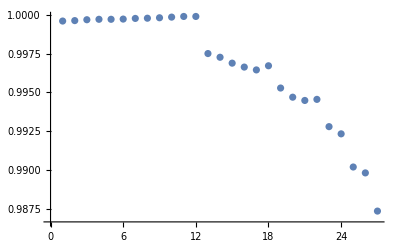

```mathematica
SplitByDays[options]//Map[FindBestBullSpread]//Select[Length[#]>0&]//Map[First]//Map[#returns&]//ListPlot
```